# Arm state visualization

## Import

```mathematica
(*ClearAll["Global`*"]
Clear["Global`*"]*)

AppendTo[$Path,"/Users/thomasbuhrmann/Library/Mathematica/Packages/LevelScheme"];
Get["LevelScheme`"];

(* Best *)
dirNameB1 = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_01_16__12_26_42"; (* Mv1234 0.994 *)
dirNameB2 = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_12_04__17_49_45"; (* Mv1234 0.992 *)
dirNameB3 = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_11_30__13_57_40"; (* Mv24 0.9918 *)
dirNameB4 = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_11_27__21_30_56"; (* Mv1234 0.9928 *)
dirNameB5 = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_11_19__21_52_30"; (* Mv1234 0.9918 *)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_03_21__13_38_43"; (* Mv1234 0.984961 Ia, Ib non-sym*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_11__17_43_03"; (* Mv1234 0.984961 Ia, Ib non-sym*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_25__14_55_44"; (* Mv1234 0.984961 Ia, Ib non-sym*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_26__15_44_55"; (* Mv1234 0.984961 Ia, Ib non-sym*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_27__00_48_28"; (* *)

(* Ablation *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_29__11_19_24"; (* Best: Inc from 13_04_27__13_03_45: 0.9897 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_30__14_01_20"; (* Like above, but without IbInterseg: 0.984 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_30__19_52_19"; (* Like above, but without IbIaExc: 0.975 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_05_23__10_26_30"; (* Like above, but no Ib at all: 0.970 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_11__15_48_55"; (* No interneurons at all, but GO sig *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_12__21_00_10"; (* No interneurons at all: 0.946 *)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_05_09__20_37_11"; (* Mv123456 Run from _19_47_32 *)

(* Dirs 8M *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_13__16_02_25"; (* 8M: 0.946. Soso.*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_15__02_07_37"; (* 8M: 0.95. Soso.*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_19__20_45_29/"; (* 0.961 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_21__11_58_38/"; (* 0.965 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_08_20__16_48_48"; (* 8M_2: 0.952. Not good. *)

(* Dirs 6M *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_15__19_15_19"; (* 6M_1: 0.967. Two moves bad. *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_16__10_04_00"; (* 6M_1 inc: 0.9723. Still two bad. *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_17__14_13_56"; (* 6M_1 inc2: 0.987. Pretty good. *)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_07_19__11_25_57/"; (* 6M_2: 0.967. Two moves bad again. *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_07_19__13_22_34/"; (* 6M_2: 0.9685. Two moves bad again. *)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_12__19_54_14/"; (*!! 6M_3: 0.989.*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_12__19_57_09/"; (* 6M_3: 0.9889.*)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_13__13_54_02"; (* 6M_3: 0.979.*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_13__13_54_11"; (* 6M_3: 0.976.*)


dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_14__10_31_25/"; (* 6M_3: 0.983. Weird hook. *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_14__00_06_01/"; (* 6M_3: 0.9825. Weird hook*)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_14__13_57_34/"; (*!! 6M_3: 0.98.*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_14__13_49_02/"; (* 6M_3: 0.9785.*)

(* Dirs 4M *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_10__08_33_31"; (*!! 4M diag: 0.9916 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_10__08_33_29"; (*!! 4M diag: 0.9914 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Dirs/0/13_07_08__16_18_21/"; (* 4M straight, slow: 0.991. Wobbly. *)
(* Mv1234 check whether 4M net works for 1234: 0.96011, 0.946. No! *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_11__15_48_55/"; 
dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_12__21_00_10/"; 

(* Energy min *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirsOlOn/0/13_07_18__18_39_18/"; 
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirsOlOn/0/13_07_19__09_46_01/"; (* network: 1.98171 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirsOlOn/0/13_07_19__10_56_15/"; (* network asymsp: 1.98431 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/R1/13_07_19__11_40_37/";(* network symsp noVelRef: 1.98415 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/R1/13_07_19__14_11_55/";(* R1 network symsp noVelRef: 1.9839 *)


dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/SpOnly/1234/13_07_19__10_06_33/"; (* Engy min PD: 1.982 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/SpOnly/1234/13_07_19__14_26_06/"; (* Engy min PD noVelRef: 0.993 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/SpOnly/1234/13_07_19__14_33_04/"; (* Engy min PD noVelRef dbgain: 0.9934 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/SpOnly/1234/13_07_19__14_46_28/"; (* Engy min PD noVelRef higher gain: 0.994 *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs/SpOnly/1234/13_07_19__14_52_51/"; 
(* Engy min PD noVelRef higher gain, exp:  *)

(* PD control multiple movements *)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs4M/13_08_20__14_11_48/"; (* 4M PD: 0.99.*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs6M/13_08_20__15_56_46/"; (* 6M PD: 0.99.*)
dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs4M/13_08_20__14_11_48/"; (* 4M PD: 0.99.*)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/IndDirs4M/13_08_20__20_53_06"; (* 4M PD min engy: *)

dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_07_21__11_58_38/"; (* 0.965 *)

(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/13_02_06__22_44_11";*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_12_21__15_16_27"; (* Mv1234 *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_12_17__17_18_17"; (* Mv1234 *)*)

(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_10_19__19_38_08"; (* Mv34 *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_10_18__14_18_53"; (* Mv12 Ext OL *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_10_17__15_14_34"; (* Mv12 Norm OL *)*)

(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_10_16__17_44_26"; (* Mv2 *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_06_10__02_25_24"; (* Mv2 *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_04_12__19_20_02/"; (* Mv2 *)*)
(*dirName = "/Users/thomasbuhrmann/Experiments/Arm/Output/12_04_13__13_03_05/"; (* Mv1 *)*)

figExpPath="~thomasbuhrmann/Dropbox/eSMCs/publications/InteractionTorques/Figures/Mathematica/";
SetDirectory[dirName];
all=Import["State.txt", "Table"];
varNames=all[[1]];
data = all[[2;;-2]];
numVars=Dimensions[varNames];
numData=Length[data]

fitXml = Import["GA_Progress.xml"];
fitness=Cases[fitXml,XMLElement["Generation",{_,"BestFitness"->fit_,_},___]->fit,Infinity];
fitness=ToExpression[fitness];
font="Arial";
```

LevelScheme scientific figure preparation system
M. A. Caprio, Department of Physics, University of Notre Dame
Comput. Phys. Commun. 171, 107 (2005)
Version 3.53 (January 10, 2013)
View color paletteVisit home page  -Graphics-

4801

## Fitness

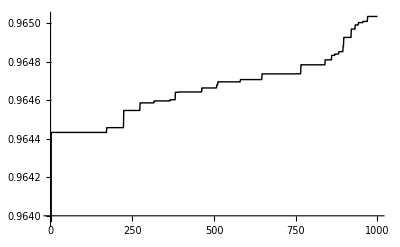

0.965034

```mathematica
fitP =ListLinePlot[fitness[[1;;Length[fitness]]],PlotStyle->Black,PlotRange->Automatic,ImageSize->400]
maxFit = Max[fitness]
```

## Robustness

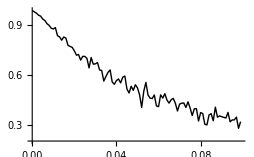

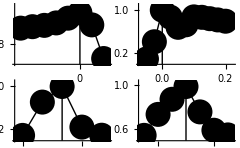

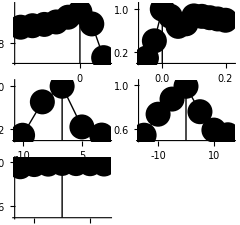

~thomasbuhrmann/Dropbox/eSMCs/publications/InteractionTorques/Figures/Mathematica/generalisation.eps

~thomasbuhrmann/Dropbox/eSMCs/publications/InteractionTorques/Figures/Mathematica/readaptConstVel.eps

```mathematica
(* Mutations *)
SetDirectory["/Users/thomasbuhrmann/Experiments/Arm/Output/13_04_29__19_27_46"];
mutFitData=Import["Fitness.txt", "Table"];
fitData = mutFitData[[2;;-2]];
mutFit =fitData[[;;,1]];
grouped = Partition[mutFit,100];
means=Mean[Transpose[grouped]];
Length[means];
x=Range[0,0.099,0.001];
Length[x];
cm=72/2.54;
robPl=ListLinePlot[Transpose[{x,means}],PlotStyle->Black,AxesOrigin->{0,0.2},ImageSize->9cm]
(*Export[figExpPath<>"robustness.svg",robPl]*)

(* Shifts *)
(*opts={PlotMarkers->None,PlotStyle->Black,FillingStyle->{Black,AbsoluteThickness[10]},Filling->Axis,BaseStyle->{FontFamily->font}};*)
opts={PlotStyle->Black,BaseStyle->{FontFamily->font},Mesh->All,MeshStyle->{PointSize[0.045],Black},BaseStyle->{FontFamily->font}};
SetOptions[LinTicks,MajorTickLength->{0.03,0},MinorTickLength->{0.01,0},ShowMinorTicks->False];

shiftFit={0.896, 0.905,0.913,0.928,0.957,0.9896,0.916,0.71};
x=Range[-25,10,5];
shiftPl=ListLinePlot[Transpose[{x,shiftFit}],AxesOrigin->{-27.5,0.95*Min[shiftFit]},PlotRange->{{-27.5,12.5},{0.95*Min[shiftFit],1.05*Max[shiftFit]}},opts,
Ticks->{LinTicks[-30,10],LinTicks[0.5,1]}, 
Epilog->{Line[{{0,0.95*Min[shiftFit]},{0,Max[shiftFit]}}]}];
shiftPl = Show[shiftPl];

(* Durations *)
durFits = {0.088,0.406,0.9896,0.8607,0.6723,0.719,0.865,0.857,0.832,0.809,0.785};
x=Range[-0.05,0.2,0.025];
durPl=ListLinePlot[Transpose[{x,durFits}],AxesOrigin->{-0.075,Min[durFits]-0.1*Max[durFits]},PlotRange->{{-0.075,0.225},{Min[durFits]-0.1*Max[durFits],1.1*Max[durFits]}},opts,
Ticks->{LinTicks[-0.05,0.2,TickLabelStep->2,TickLabelStart->1],
LinTicks[0,1,TickLabelStep->2,TickLabelStart->1]}, 
Epilog->{Line[{{0,Min[durFits]-0.1*Max[durFits]},{0,Max[durFits]}}]}];

(* Amplitudes *)
ampFits = {0.0818,0.7,0.9896,0.2356,0.085};
x=Range[-10,10,5];
ampPl=ListLinePlot[Transpose[{x,ampFits}],AxesOrigin->{-12,Min[ampFits]-0.1*Max[ampFits]},PlotRange->{{-12,12},{Min[ampFits]-0.1*Max[ampFits],1.1*Max[ampFits]}},opts,
Ticks->{LinTicks[-10,10],
LinTicks[0,1,TickLabelStep->2,TickLabelStart->1]}, 
Epilog->{Line[{{0,Min[ampFits]-0.1*Max[ampFits]},{0,Max[ampFits]}}]}];

(* Const velocity (changing duration and amplitude in proportion) *)
velFits = {0.54, 0.733,0.872,0.9896,0.756,0.587,0.544};
x=Range[-15,15,5];
velPl=ListLinePlot[Transpose[{x,velFits}],AxesOrigin->{-17,Min[velFits]-0.05*Max[velFits]},PlotRange->{{-17,17},{Min[velFits]-0.05*Max[velFits],1.05*Max[velFits]}},opts,
Ticks->{LinTicks[-15,15,TickLabelStep->2,TickLabelStart->1],
LinTicks[0.5,1,TickLabelStep->2,TickLabelStart->1]}, 
Epilog->{Line[{{0,Min[velFits]-0.05*Max[velFits]},{0,Max[velFits]}}]}];

(* Readapted Const velocity (changing duration and amplitude in proportion) *)
revelFits = {0.959, 0.979,0.983,0.9896,0.988,0.987,0.984};
x=Range[-15,15,5];
revelPl=ListLinePlot[Transpose[{x,revelFits}],AxesOrigin->{-17,Min[velFits]-0.05*Max[velFits]},PlotRange->{{-17,17},{Min[velFits]-0.05*Max[velFits],1.05*Max[velFits]}},opts,Ticks->{LinTicks[-15,15,TickLabelStep->2,TickLabelStart->1],
LinTicks[0.5,1,TickLabelStep->2,TickLabelStart->1]},
Epilog->{Line[{{0,Min[velFits]-0.05*Max[revelFits]},{0,Max[revelFits]}}]} ];

general=Show[GraphicsGrid[{{shiftPl, durPl},{ampPl,velPl}}], ImageSize->8.5cm]
readapt=Show[GraphicsGrid[{{shiftPl, durPl},{ampPl,velPl},{revelPl}}], ImageSize->8.5cm]
(*readapt = Show[revelPl, ImageSize->8.5cm]*)

Export[figExpPath<>"generalisation.eps",general]
Export[figExpPath<>"readaptConstVel.eps",readapt]

SetDirectory[dirName];
```

## Config

```mathematica
dt = 0.001;
leadIn = 0.1;
leadOut = 0.2;
moveDuration = 0.3;
bestFitDelay = -0.0 / dt;
(*plotDuration = (moveDuration+leadOut/3) / dt;*)

trialDuration = leadIn+moveDuration+leadOut;
frontLead =0.1;
backLead = 1.0*leadOut;

numData/(trialDuration/dt)
Round[numData/(trialDuration/dt)]
numTrials=Round[numData/(trialDuration/dt)]

SetTrial[trial_]:=Module[{},
t0=2 +((leadIn-frontLead+ (trial*trialDuration))/dt);
tn=-2 +t0+(leadIn + moveDuration+backLead)/dt;
time=Range[tn-t0]*dt;
];

SetTrial[0];

padds={{20,40},{20,20}};
plotOptions = {PlotJoined->True, PlotRange->All, ImagePadding->padds};
graphicsWidth = 600;
font="Arial";
SetOptions[Plot,BaseStyle->{FontFamily->font}];
pad={{20,10},{15,10}};
```

8.00167

8

8

## Functions

```mathematica
NtoI[name_]:=Position[varNames, name][[1,1]];
NtoD[name_, delay_:0]:=Table[data[[i,NtoI[name]]],{i,t0+delay,tn-1+delay}];
TimePlot[name_, options_, delay_:0,Scale_:1] := ListLinePlot[Transpose[{time,Scale*NtoD[name, delay]}], Join[options,plotOptions]];
TimePlotD[data_, options_, Scale_:1] := ListLinePlot[Transpose[{time,Scale*data}], Join[plotOptions,options]];

Maxima[x_,time_]:=Module[{max,peaks, times},
max = 1+Position[Differences[Sign[Differences[x]]],-2];
peaks = Extract[x, max];
times = Extract[time,max];
maxima = Transpose[{Flatten[times],peaks}];
maxima
]

Minima[x_,time_]:=Module[{min,peaks, times},
min = 1+Position[Differences[Sign[Differences[-x]]],-2];
peaks = -Extract[-x, min];
times = Extract[time,min];
minima = Transpose[{Flatten[times],peaks}];
minima
]

TimePlotMaxima[x_,time_, opt_:{}]:= ListPlot[Maxima[x,time],opt]
TimePlotMinima[x_,time_,opt_:{}]:= ListPlot[Minima[x,time],opt]
TimePlotOptima[x_, time_, opt1_:{},opt2_:{}]:=Module[{ma,mi},
ma=TimePlotMaxima[x, time,Join[{PlotStyle->Black},opt1]];
mi=TimePlotMinima[x,time,Join[{PlotStyle->Red},opt2]];
mami=Show[ma, mi];
mami
]

Shift[list_,del_]:=Module[{},
res=Drop[list,del];
res = If[del<0,
PadLeft[res,Length[list],res[[1]]],
PadRight[res,Length[list],res[[Length[res]]]]
]
];

(*l=Range[0,10]
l4=Shift[l,-2]*)
```

## All trajectories

28.3465

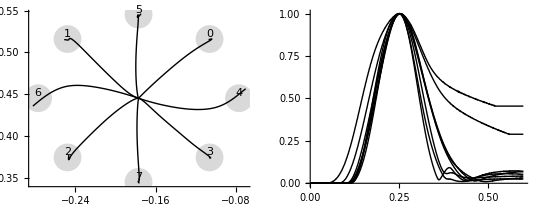

~thomasbuhrmann/Dropbox/eSMCs/publications/InteractionTorques/Figures/Mathematica/TrajStar4M2.eps

```mathematica
PlotTraj[trial_]:=Module[{},
SetTrial[trial];
x = NtoD["x"];
y = NtoD["y"];
elbX=NtoD["elbX"];
elbY=NtoD["elbY"];
desX=NtoD["desX"];
desY=NtoD["desY"];
positions=Transpose[{x,y}];
elbPositions=Transpose[{elbX,elbY}];
desPositions=Transpose[{desX,desY}];
cartesianPos=ListLinePlot[positions,plotOptions,PlotStyle->{Black},AxesOrigin->{Min[x],Min[y]}];
pos0=First[positions];
elb0=First[elbPositions];
posN=Last[positions];
elbN=Last[elbPositions];
startPos = Graphics[{PointSize[Large],Point[pos0]}];
elbStartPos = Graphics[{LightGray,PointSize[Large],Point[elb0]}];
desEndPos=Graphics[{LightGray,PointSize[0.05],Point[Last[desPositions]]}];
label=Graphics[Text[trial,Last[desPositions],{0,-2}]];
lower0=Graphics[{LightGray,Line[{elb0, pos0}]}];
upper0=Graphics[{LightGray,Line[{{0,0}, elb0}]}];
lowerN=Graphics[{LightGray,Line[{elbN, posN}]}];
upperN=Graphics[{LightGray,Line[{{0,0}, elbN}]}];
optimal = Graphics[{LightGray,Dashed,Line[{pos0, Last[desPositions]}]}];
Show[(*elbStartPos,lower0,upper0,*)(*lowerN,upperN, optimal,*) (*startPos,*)desEndPos,cartesianPos,label,BaseStyle->{FontFamily->font}]
]

TangVels[trial_] :=Module[{},
SetTrial[trial];
x = NtoD["x"];
y = NtoD["y"];
positions=Transpose[{x,y}];
vels= Map[Norm,Differences[positions]]/dt;
vels=PadRight[vels,Length[time],Last[vels]]
]

MaxTangVelPos[trial_]:=Module[{}, tangVels = TangVels[trial];Position[tangVels,Max[tangVels]][[1]] ]
maxVelPos = Flatten[Map[MaxTangVelPos,Range[0,numTrials-1,1]]];
velOff = maxVelPos-Min[maxVelPos];

PlotTangVels[trial_]:=Module[{},
vels=TangVels[trial];
(* Shift so peaks coincide *)
vels = Drop[vels,velOff[[trial+1]]];
vels=PadRight[vels,Length[vels]+velOff[[trial+1]], Last[vels]];
(* Scale to same peak *)
maxVel =Max[Map[Norm,vels]];
vels = vels / maxVel;
col = Black;(*If[trial < 2,Black,Gray];*)
ln = {};(*If[EvenQ[trial],{},Dashed];*)
tangVel=TimePlotD[vels,{PlotStyle->{col, ln},BaseStyle->{FontFamily->font}}]
];

PlotAngles[trial_,mmin_:50,mmax_:100]:=Module[{},
SetTrial[trial];
shdAng=NtoD["angleShoulder"]/Degree;
shdAngDes=NtoD["desShoulder"]/Degree;
shdAngCom =NtoD["comShoulder"]/Degree;
elbAng=NtoD["angleElbow"]/Degree;
elbAngDes=NtoD["desElbow"]/Degree;
elbAngCom =NtoD["comElbow"]/Degree;
min=Min[Min[elbAng],Min[shdAng]]*0.9;
max=Max[Max[elbAng],Max[shdAng]]*1.1;
shdPl= TimePlotD[shdAng,{PlotStyle->{Black}}];
shdPlDes= TimePlotD[shdAngDes,{PlotStyle->{LightGray,Thick}}];
shdPlCom= TimePlotD[shdAngCom,{PlotStyle->{Black,Dashed}}];
elbPl= TimePlotD[elbAng,{PlotStyle->{Black}}];
elbPlDes= TimePlotD[elbAngDes,{PlotStyle->{LightGray,Thick}}];
elbPlCom= TimePlotD[elbAngCom,{PlotStyle->{Black,Dashed}}];
Show[elbPlDes, shdPlDes,shdPl,elbPl,shdPlCom,elbPlCom,PlotRange->{{0,0.6},{min,max}},AxesOrigin->{0,min},BaseStyle->{FontFamily->font},ImagePadding->pad,
Ticks->{LinTicks[0,0.6,TickLabelStep->2,TickLabelStart->1],
LinTicks[mmin,mmax,TickLabelStep->2,TickLabelStart->1]} ]
];

PlotAngVels[trial_]:=Module[{},
SetTrial[trial];
shdVel=NtoD["velocityShoulder"]/Degree;
elbVel=NtoD["velocityElbow"]/Degree;
shdPl= TimePlotD[shdVel,{PlotStyle->{Black}}];
elbPl= TimePlotD[elbVel,{PlotStyle->{Black,Dashed}}];
Show[elbPl, shdPl]
];

(* Forces applied at joints, total is more or less acceleration *)
PlotTrqsElb[trial_,min_:-10,max_:10]:=Module[{},
SetTrial[trial];
itD = -NtoD["interactionElbow"] - NtoD["coriolisElbow"];
msD = NtoD["torqueElbow"];
totalD = msD +itD;
total = TimePlotD[totalD,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent}}];
trq= TimePlotD[msD,{PlotStyle->Black}];
it = TimePlotD[itD,{PlotStyle->{Black,Dashed}}];
mmin = 1.1*Min[{Min[itD],Min[msD],Min[totalD]}];
trqs = Show[total,trq, it,PlotRange->{{0,0.6},{mmin,Automatic}},AxesOrigin->{0,mmin},BaseStyle->{FontFamily->font},ImagePadding->pad,
Ticks->{LinTicks[0,0.6,TickLabelStep->2,TickLabelStart->1],
LinTicks[min,max,TickLabelStep->2,TickLabelStart->0]} ]
]

PlotAMNElb[trial_]:=Module[{},
SetTrial[trial];
aMNElbAgP =  TimePlot["reflexElbMNAg",{PlotStyle->Black}];
aMNElbAnP =  TimePlot["reflexElbMNAn",{PlotStyle->{Black,Dashed}}];
aMNElbPlot =Show[aMNElbAgP,aMNElbAnP ]
]

PlotAMNShd[trial_]:=Module[{},
SetTrial[trial];
aMNShdAgP =  TimePlot["reflexShdMNAg",{PlotStyle->Black}];
aMNShdAnP =  TimePlot["reflexShdMNAn",{PlotStyle->{Black,Dashed}}];
aMNShdPlot =Show[aMNShdAgP,aMNShdAnP ]
]

PlotTrqMElb[trial_]:=Module[{},
SetTrial[trial];
elbAgTrq = NtoD["ElbowFlexorTorque"];
elbAnTrq = NtoD["ElbowExtensorTorque"];
elbNetTrq = elbAgTrq - elbAnTrq;
max = Max[Max[Abs[elbAgTrq]],Max[Abs[elbAnTrq]],Max[Abs[elbNetTrq]]];
elbAgTorqueP = TimePlotD[elbAgTrq,{PlotStyle->{Black}, PlotRange->{Automatic,{-max*1.1, max*1.1}}}];
elbAnTorqueP = TimePlotD[elbAnTrq, {PlotStyle->{Black,Dashed}, PlotRange->{Automatic,{-max*1.1, max*1.1}}},-1];
elbNetTrqP = TimePlotD[elbNetTrq,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent}, PlotRange->{Automatic,{-max*1.1, max*1.1}}}];
elbTrq = Show[elbNetTrqP,elbAgTorqueP,elbAnTorqueP, PlotRange->{Automatic,{-max, max}}]
]

PlotTrqMShd[trial_]:=Module[{},
SetTrial[trial];
shdAgTrq = NtoD["ShoulderFlexorTorque"];
shdAnTrq = NtoD["ShoulderExtensorTorque"];
shdNetTrq = shdAgTrq - shdAnTrq;
max = Max[Max[Abs[shdAgTrq]],Max[Abs[shdAnTrq]],Max[Abs[shdNetTrq]]];
shdAgTorqueP = TimePlotD[shdAgTrq,{PlotStyle->{Black}, PlotRange->{Automatic,{-max*1.1, max*1.1}},ImageSize->2cm}];
shdAnTorqueP = TimePlotD[shdAnTrq, {PlotStyle->{Black,Dashed}, PlotRange->{Automatic,{-max*1.1, max*1.1}}},-1];
shdNetTrqP = TimePlotD[shdNetTrq,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent}, PlotRange->{Automatic,{-max*1.1, max*1.1}}}];
shdTrq = Show[shdNetTrqP,shdAgTorqueP,shdAnTorqueP,PlotRange->{Automatic,{-max, max}}]
]

PlotTrqsShd[trial_,min_:-10,max_:10]:=Module[{},
SetTrial[trial];
itD = -NtoD["interactionShoulder"] - NtoD["coriolisShoulder"];
msD = NtoD["torqueShoulder"];
totalD = msD +itD;
total = TimePlotD[totalD,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent},ImageSize->22cm}];
trq= TimePlot["torqueShoulder",{PlotStyle->Black}];
it = TimePlotD[itD,{PlotStyle->{Black,Dashed}}];
mmin =1.1* Min[{Min[itD],Min[msD],Min[totalD]}];
mmax =1.1* Max[{Max[itD],Max[msD],Max[totalD]}];
trqs = Show[total,trq, it,PlotRange->{{0,0.6},{mmin,mmax}},AxesOrigin->{0,mmin},BaseStyle->{FontFamily->font},ImagePadding->pad,
Ticks->{LinTicks[0,0.6,TickLabelStep->2,TickLabelStart->1],
LinTicks[min,max,TickLabelStep->2,TickLabelStart->0,ShowMinorTicks->False]}]
]

trajsPl = Show[Table[PlotTraj[i],{i,0,numTrials-1}], Axes->True,AxesOrigin->{-0.45,0.25},ImagePadding->pad,AxesStyle->Thickness[.002]];


tangVelsPl=Show[Table[PlotTangVels[i],{i,0,numTrials-1}](*AspectRatio->1,*), ImagePadding->pad,AxesStyle->Thickness[.002]];

cm=72/2.54
angAndVel=Show[GraphicsRow[{trajsPl, tangVelsPl}],ImageSize->19cm]

Export[figExpPath<>"TrajStar4M2.eps",trajsPl]
(*Export[figExpPath<>"c1TrajAndVelNoIbIs.eps",angAndVel]*)

(*GraphicsGrid[Partition[Table[PlotAngles[i],{i,0,numTrials-1}],2],ImageSize->600]*)
(*GraphicsGrid[Partition[Table[PlotAngVels[i],{i,0,numTrials-1}],2],ImageSize->600]*)
(*GraphicsGrid[Partition[Table[PlotTrqsElb[i],{i,0,numTrials-1}],2],ImageSize->600]*)
tr1=0;
tr2=1;

(*mv12=GraphicsGrid[{{PlotAngles[tr1,40,90],PlotAngles[tr2,40,90]},{PlotTrqsElb[tr1,-2,2], PlotTrqsElb[tr2,-2,1]},{PlotTrqsShd[tr1,-12,12], PlotTrqsShd[tr2,-7,7]}},ImageSize->19cm,AxesStyle->Thickness[.002]]

mn12=GraphicsGrid[{{PlotAMNElb[tr1],PlotAMNShd[tr1],PlotAMNElb[tr2],PlotAMNShd[tr2]},
{PlotTrqMElb[tr1],PlotTrqMShd[tr1],PlotTrqMElb[tr2],PlotTrqMShd[tr2]}},ImageSize->22cm,AxesStyle->Thickness[.002]]

tr1=2;
tr2=3;
mv34=GraphicsGrid[{{PlotAngles[tr1],PlotAngles[tr2]},{PlotTrqsElb[tr1], PlotTrqsElb[tr2]},{PlotTrqsShd[tr1], PlotTrqsShd[tr2]}},ImageSize->19cm]


Export[figExpPath<>"c1AngleAndTorquesMv12.eps",mv12]
(*Export[figExpPath<>"c1AngleAndTorquesMv34.svg",mv34]
Export[figExpPath<>"aMN-Trq.pdf",mn12]*)
*)
```

```mathematica
TrajErr[trial_,del_:0] := Module[{},
SetTrial[trial];
(*Only actual movement, without leanIn or leadOut *)
tt0 = IntegerPart[leadIn/(2*dt)];
tt1 = -IntegerPart[leadOut/(2*dt)];
x = NtoD["x"][[tt0;;tt1]];
y = NtoD["y"][[tt0;;tt1]];
desX = Shift[NtoD["desX"][[tt0;;tt1]],del];
desY = Shift[NtoD["desY"][[tt0;;tt1]],del];
(*desX=NtoD["desX"][[tt0+del;;tt1+del]];*)
(*desY=NtoD["desY"][[tt0+del;;tt1+del]];*)
positions = Transpose[{x, y}];
desPositions = Transpose[{desX, desY}]; 
d=EuclideanDistance[desPositions[[1]],desPositions[[Length[desPositions]]] ];
se=MapThread[EuclideanDistance, {positions, desPositions}];
mse=Mean[se]*1000
];

maxShift=50;
TrajErrLag[trial_] := Module[{},
errs=Table[TrajErr[trial,d],{d,-maxShift,maxShift}];
Print[errs];
minErr=Min[errs];
minPos = Position[errs,minErr];
Print[-maxShift+minPos-1];
minErr
];

MaxRotVel[trial_] := Module[{},
SetTrial[trial];
elbVel = NtoD["velocityElbow"]/Degree;
shdVel = NtoD["velocityShoulder"]/Degree;
res = {Max[Abs[elbVel]], Max[Abs[shdVel]]}
]

(*t1=Table[TrajErr[i,0],{i,0,numTrials-1}]*)

t1l=Table[TrajErrLag[i],{i,0,numTrials-1}]
Mean[t1l]
t2=Table[Max[TangVels[i]],{i,0,numTrials-1}]
t3=Table[MaxRotVel[i],{i,0,numTrials-1}]
```

{5.58338,5.36975,5.15682,4.94467,4.73344,4.52324,4.31425,4.10666,3.90069,3.69661,3.49476,3.29555,3.09948,2.90716,2.71943,2.53737,2.36271,2.19875,2.04637,1.90613,1.77976,1.66987,1.58019,1.51596,1.48414,1.49267,1.54746,1.64813,1.78681,1.95222,2.13459,2.32758,2.52751,2.73225,2.94043,3.15116,3.36381,3.57795,3.79327,4.00953,4.22656,4.44421,4.66239,4.88102,5.10001,5.31933,5.53893,5.75876,5.97881,6.19903,6.41942,6.63996,6.86062,7.0814,7.30228,7.52325,7.7443,7.96544,8.18664,8.4079,8.62922,8.8506,9.07202,9.29349,9.515,9.73655,9.95813,10.1797,10.4014,10.6231,10.8448,11.0665,11.2882,11.51,11.7318,11.9536,12.1755,12.3973,12.6192,12.841,13.0629,13.2848,13.5068,13.7287,13.9506,14.1726,14.3946,14.6165,14.8385,15.0605,15.2825,15.5045,15.7266,15.9486,16.1706,16.3927,16.6147,16.8368,17.0588,17.2809,17.503}

{{-26}}

{10.7227,10.5092,10.2959,10.0826,9.86932,9.65617,9.44311,9.23013,9.01725,8.80447,8.59179,8.37924,8.1668,7.95451,7.74237,7.53039,7.3186,7.10701,6.89565,6.68455,6.47374,6.26325,6.05314,5.84344,5.63423,5.42557,5.21754,5.01027,4.80387,4.5985,4.39436,4.1917,3.99083,3.79217,3.59624,3.40371,3.21547,3.03263,2.85658,2.68897,2.53171,2.38682,2.25629,2.14196,2.04548,1.9684,1.9123,1.87891,1.87025,1.88931,1.94352,2.03288,2.14851,2.28511,2.43835,2.60461,2.78101,2.96534,3.15587,3.35131,3.5507,3.75327,3.95844,4.16577,4.3749,4.58555,4.79749,5.01054,5.22454,5.43937,5.65491,5.8711,6.08784,6.30508,6.52276,6.74084,6.95926,7.178,7.39703,7.61632,7.83584,8.05557,8.2755,8.4956,8.71586,8.93626,9.1568,9.37747,9.59824,9.81912,10.0401,10.2612,10.4823,10.7035,10.9248,11.1461,11.3675,11.589,11.8105,12.0321,12.2536}

{{-2}}

{8.14723,7.93337,7.71982,7.50661,7.29378,7.08136,6.8694,6.65793,6.44702,6.23672,6.02709,5.81824,5.61023,5.40319,5.19723,4.9925,4.78918,4.58746,4.38761,4.18991,3.99471,3.80246,3.61368,3.42902,3.24931,3.07555,2.90902,2.75134,2.60462,2.47169,2.35688,2.26757,2.20481,2.17002,2.16494,2.19046,2.24607,2.32964,2.43773,2.56636,2.71164,2.87021,3.03932,3.21682,3.40101,3.59061,3.7846,3.9822,4.1828,4.38591,4.59113,4.79815,5.00672,5.21661,5.42765,5.6397,5.85262,6.06633,6.28072,6.49572,6.71126,6.92729,7.14376,7.36063,7.57785,7.7954,8.01324,8.23136,8.44972,8.6683,8.88709,9.10608,9.32524,9.54456,9.76403,9.98365,10.2034,10.4233,10.6432,10.8633,11.0835,11.3038,11.5242,11.7446,11.9651,12.1857,12.4064,12.6271,12.8479,13.0688,13.2897,13.5106,13.7316,13.9527,14.1738,14.3949,14.6161,14.8373,15.0586,15.2799,15.5012}

{{-16}}

{7.67679,7.45709,7.23767,7.0186,6.79992,6.58168,6.36395,6.1468,5.93029,5.71448,5.49946,5.28528,5.07201,4.85972,4.64849,4.4384,4.22953,4.02199,3.81588,3.61134,3.40851,3.20758,3.00876,2.8123,2.61849,2.42773,2.2405,2.05743,1.87941,1.70767,1.54404,1.39142,1.25347,1.13456,1.04095,0.981836,0.974298,1.03428,1.17548,1.37341,1.58563,1.80195,2.02008,2.23924,2.45905,2.67932,2.89992,3.12077,3.34182,3.56302,3.78435,4.00579,4.22732,4.44892,4.67058,4.8923,5.11406,5.33587,5.55771,5.77959,6.00149,6.22342,6.44537,6.66734,6.88933,7.11133,7.33335,7.55538,7.77743,7.99949,8.22155,8.44363,8.66571,8.8878,9.1099,9.33201,9.55412,9.77624,9.99837,10.2205,10.4426,10.6648,10.8869,11.1091,11.3312,11.5534,11.7755,11.9977,12.2198,12.442,12.6642,12.8863,13.1085,13.3307,13.5529,13.775,13.9972,14.2194,14.4416,14.6638,14.8859}

{{-14}}

{8.99603,9.07439,9.15839,9.24808,9.3435,9.44467,9.55162,9.66433,9.78279,9.90696,10.0368,10.1722,10.3131,10.4594,10.6108,10.7674,10.9287,11.0948,11.2652,11.4398,11.6182,11.8003,11.9857,12.1741,12.3652,12.5588,12.7545,12.9522,13.1516,13.3526,13.5548,13.7582,13.9627,14.1682,14.3745,14.5817,14.7896,14.9983,15.2076,15.4175,15.628,15.839,16.0505,16.2626,16.475,16.6879,16.9012,17.1149,17.3289,17.5433,17.758,17.9731,18.1884,18.4039,18.6198,18.8359,19.0523,19.2688,19.4856,19.7026,19.9198,20.1372,20.3548,20.5726,20.7905,21.0086,21.2269,21.4453,21.6638,21.8825,22.1013,22.3202,22.5393,22.7584,22.9777,23.1971,23.4166,23.6362,23.8559,24.0757,24.2956,24.5155,24.7356,24.9557,25.1759,25.3962,25.6165,25.8369,26.0574,26.2779,26.4985,26.7192,26.9399,27.1607,27.3815,27.6024,27.8233,28.0443,28.2653,28.4864,28.7075}

{{-50}}

{11.7973,11.586,11.3745,11.1629,10.9511,10.7391,10.527,10.3148,10.1024,9.88988,9.67722,9.46444,9.25154,9.03853,8.82542,8.61223,8.39896,8.18565,7.97229,7.75893,7.54559,7.3323,7.11911,6.90606,6.69324,6.48072,6.26861,6.05708,5.84632,5.63664,5.42846,5.22234,5.01908,4.8196,4.62493,4.43604,4.25384,4.07918,3.91282,3.7555,3.60792,3.47074,3.34459,3.23006,3.1277,3.03799,2.9614,2.89827,2.84891,2.8135,2.79214,2.78482,2.79145,2.81188,2.84589,2.89325,2.9537,3.02701,3.11293,3.21123,3.32172,3.44421,3.57856,3.72471,3.88267,4.05263,4.23517,4.43131,4.63959,4.85387,5.07054,5.28843,5.50707,5.72625,5.94582,6.16571,6.38585,6.60619,6.82672,7.0474,7.26821,7.48913,7.71015,7.93125,8.15244,8.3737,8.59502,8.81639,9.03782,9.25929,9.48081,9.70237,9.92396,10.1456,10.3672,10.5889,10.8106,11.0324,11.2541,11.4759,11.6977}

{{1}}

{14.0693,14.2589,14.4509,14.645,14.8412,15.0392,15.239,15.4403,15.643,15.8471,16.0523,16.2586,16.4659,16.6741,16.8832,17.0929,17.3034,17.5144,17.7261,17.9383,18.1509,18.364,18.5775,18.7915,19.0057,19.2204,19.4353,19.6505,19.8661,20.0819,20.2979,20.5142,20.7307,20.9475,21.1645,21.3816,21.599,21.8165,22.0343,22.2522,22.4702,22.6884,22.9068,23.1253,23.3439,23.5627,23.7816,24.0006,24.2198,24.439,24.6584,24.8779,25.0974,25.3171,25.5369,25.7567,25.9767,26.1967,26.4168,26.6369,26.8572,27.0775,27.2979,27.5184,27.7389,27.9595,28.1801,28.4008,28.6215,28.8423,29.0632,29.2841,29.5051,29.7261,29.9471,30.1682,30.3893,30.6105,30.8317,31.053,31.2743,31.4956,31.7169,31.9383,32.1597,32.3812,32.6026,32.8242,33.0457,33.2672,33.4888,33.7104,33.9321,34.1537,34.3754,34.5971,34.8188,35.0405,35.2623,35.4841,35.7058}

{{-50}}

{10.5153,10.2965,10.0778,9.85904,9.64032,9.42162,9.20293,8.98427,8.76563,8.547,8.3284,8.10982,7.89127,7.67274,7.45425,7.23579,7.01737,6.799,6.58068,6.36243,6.14424,5.92615,5.70817,5.49031,5.27261,5.05518,4.83799,4.62111,4.40464,4.18872,3.9736,3.75974,3.5481,3.34053,3.13904,2.94504,2.75981,2.58456,2.42047,2.26864,2.13011,2.00583,1.89667,1.80335,1.72647,1.66652,1.6238,1.59849,1.59068,1.60043,1.62787,1.67324,1.73703,1.82007,1.92381,2.05103,2.2103,2.40528,2.61485,2.82949,3.04645,3.26472,3.48381,3.70347,3.92355,4.14395,4.3646,4.58545,4.80646,5.0276,5.24886,5.47022,5.69166,5.91318,6.13476,6.35639,6.57807,6.7998,7.02156,7.24336,7.46519,7.68705,7.90894,8.13085,8.35277,8.57472,8.79668,9.01867,9.24066,9.46267,9.68469,9.90672,10.1288,10.3508,10.5729,10.7949,11.017,11.2391,11.4612,11.6833,11.9054}

{{-2}}

{1.48414,1.87025,2.16494,0.974298,8.99603,2.78482,14.0693,1.59068}

4.24181

{0.626554,0.720345,0.664606,0.649878,0.465022,0.768547,0.41676,0.747324}

{{84.0095,22.4346},{209.172,123.253},{59.3647,47.439},{141.748,103.745},{60.3745,78.0566},{220.408,77.1962},{71.7128,72.0969},{162.833,40.554}}

```mathematica
Mean[{1.48414,1.87025,2.16494,0.974298,8.99603,2.78482,1.59068,14.06928405}]
```

4.24181

## Draw arm kinematics

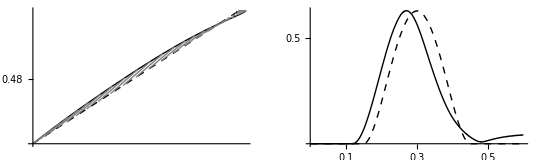

```mathematica
SetTrial[0];

(* Joint trajectories *)
elbAng=NtoD["angleElbow"]/Degree;
elbDes = NtoD["desElbow"]/Degree;
elbCom = NtoD["comElbow"]/Degree;
angleElb =TimePlotD[elbAng,{PlotStyle->{Black}, AxesLabel->{"time","angle"}}];
desAngleElb = TimePlotD[elbDes,{PlotStyle->{Black,Dashed}, AxesLabel->{"time","angle"}}];
comAngleElb = TimePlotD[elbCom,{PlotStyle->{Gray}, AxesLabel->{"time","angle"}}];

shdAng=NtoD["angleShoulder"]/Degree;
shdDes = NtoD["desShoulder"]/Degree;
shdCom = NtoD["comShoulder"]/Degree;
angleShd= TimePlotD[shdAng,{PlotStyle->{Black}}];
desAngleShd = TimePlotD[shdDes,{PlotStyle->{Black,Dashed}, AxesLabel->{"time","angle"}}];
comAngleShd = TimePlotD[shdCom,{PlotStyle->{Gray}, AxesLabel->{"time","angle"}}];
elbow = Show[angleElb, desAngleElb, comAngleElb];
shoulder = Show[angleShd, desAngleShd, comAngleShd];

(* Calculate derivatives *)
accScale = 10;

velElb= TimePlot["velocityElbow",{PlotStyle->{Black}, AxesLabel->{"time","velocity"}}];
desVelElbD = Differences[NtoD["desElbow", bestFitDelay]]/dt;
desVelElbD = PadRight[desVelElbD,Length[time],Last[desVelElbD]];
desVelElb = TimePlotD[desVelElbD,{PlotStyle->{Black,Dashed}}];
desAccElbD = Differences[desVelElbD]/dt/accScale;
desAccElbD = PadRight[desAccElbD,Length[time],Last[desAccElbD]];
desAccElbD = MovingAverage[desAccElbD,3];
desAccElbD = PadRight[desAccElbD,Length[time],Last[desAccElbD]];
desAccElb = TimePlotD[desAccElbD,{PlotStyle->{Gray}}];

velShd= TimePlot["velocityShoulder",{PlotStyle->{Black}}];
desVelShdD = Differences[NtoD["desShoulder", bestFitDelay]]/dt;
desVelShdD = Append[desVelShdD,desVelShdD[[Length[desVelShdD]]]];
desVelShd = TimePlotD[desVelShdD,{PlotStyle->{Black,Dashed}}];
desAccShdD = Differences[desVelShdD]/dt/accScale;
desAccShdD = PadRight[desAccShdD,Length[time],Last[desAccShdD]];
desAccShdD = MovingAverage[desAccShdD,3];
desAccShdD = PadRight[desAccShdD,Length[time],Last[desAccShdD]];
desAccShd = TimePlotD[desAccShdD,{PlotStyle->{Gray}}];

velsElb = Show[velElb, desVelElb, desAccElb];
velsShd = Show[velShd, desVelShd, desAccShd];
vels = Show[velElb,velShd];

(* Forces applied at joints, total is more or less acceleration *)
itElbD = -NtoD["interactionElbow"] - NtoD["coriolisElbow"];
msElbD = NtoD["torqueElbow"];
totalElbD = msElbD +itElbD;
totalElb = TimePlotD[totalElbD,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent}, AxesLabel->{"time","forceElb"}}];
trqElb= TimePlot["torqueElbow",{PlotStyle->Black}];
itElb = TimePlotD[itElbD,{PlotStyle->{Black,Dashed}}];
(*opttotalP = TimePlotOptima[totalElbD, time];
optitP = TimePlotOptima[itElbD, time];
optmsP = TimePlotOptima[msElbD, time];*)
trqsElb = Show[totalElb,trqElb, itElb(*, opttotalP,optitP, optmsP*)];

(*Maxima[totalElbD,time][[1]]*)

itShdD = -NtoD["interactionShoulder"] - NtoD["coriolisShoulder"];
totalShdD = NtoD["torqueShoulder"]+itShdD;
totalShd = TimePlotD[totalShdD,{Filling->Axis,FillingStyle->LightGray,PlotStyle->{Transparent},AxesLabel->{"time","forceShd"}}];
trqShd= TimePlot["torqueShoulder",{PlotStyle->Black}];
itShd = TimePlotD[itShdD,{PlotStyle->{Black,Dashed}}];
trqsShd = Show[totalShd,trqShd, itShd];


(* Effector space trajectories, i.e. cartesian position *)
xPos = TimePlot["x",{PlotStyle->{Black}, AxesLabel->{"time","x,y"}}];
desX = TimePlot["desX",{PlotStyle->{Black, Dashed}, AxesLabel->{"time","x,y"}}, bestFitDelay];
comX = TimePlot["comX",{PlotStyle->{Gray}, AxesLabel->{"time","x,y"}}];
yPos = TimePlot["y",{PlotStyle->{Black}}];
desY = TimePlot["desY",{PlotStyle->{Black, Dashed}, AxesLabel->{"time","x,y"}}, bestFitDelay];
comY = TimePlot["comY",{PlotStyle->{Gray}, AxesLabel->{"time","x,y"}}];
pos = Show[xPos,yPos, desX, desY];
posX = Show[xPos, desX, comX];
posY = Show[yPos, desY, comY];

(* XY plot *)
x = NtoD["x"];
y = NtoD["y"];
positions=Transpose[{x,y}];
cartesianPos=ListLinePlot[positions,plotOptions,PlotStyle->Black,AxesOrigin->{Min[x],Min[y]}, AxesLabel->{"x","y"}];
startPos = Graphics[{PointSize[Large],Point[First[positions]]}];
desX = Shift[NtoD["desX"],-50];
desY = Shift[NtoD["desY"],-50];
desPos = Transpose[{desX,desY}];
desCartPos = ListLinePlot[desPos,plotOptions,PlotStyle->{Black,Dashed},AxesOrigin->{Min[x],Min[y]}, AxesLabel->{"x","y"}];
sample=Table[{positions[[i]],desPos[[i]]},{i,50,Length[desPos],10}];
paral=Graphics[{Gray,Line[sample]}];
xyPos = Show[cartesianPos,desCartPos,paral];

(* Calculate tangential velocity *)
vels= Map[Norm,Differences[positions]]/dt;
vels=PadRight[vels,Length[time],Last[vels]];
tangVel=TimePlotD[vels,{PlotStyle->{Black},AxesLabel->{"time","vel"}}];
desVels = Map[Norm,Differences[desPos]]/dt;
desVels = PadRight[desVels,Length[time],Last[desVels]];
tangDesVel = TimePlotD[desVels,{PlotStyle->{Black,Dashed},AxesLabel->{"time","vel"}}];
cartVels = Show[tangVel,tangDesVel]; 

(*(gg=GraphicsGrid[{{pos,angles,vels},{accs,trqsElb, trqsShd}}, ImageSize->{1200}]*)
armPlots=GraphicsGrid[{{xyPos, cartVels},{posX, posY},{elbow, shoulder}, {velsElb,velsShd}, {trqsElb,trqsShd}}, ImageSize->graphicsWidth];

posVelPl = GraphicsRow[{
Show[xyPos,Ticks->{LinTicks[-0.15,0.2,TickLabelStep->2,TickLabelStart->1],
LinTicks[0.45,0.53,TickLabelStep->2,TickLabelStart->1]},AxesLabel->{}], 
Show[cartVels,Ticks->{LinTicks[0,0.6,TickLabelStep->2,TickLabelStart->1],
LinTicks[0,2,TickLabelStep->2,TickLabelStart->1]},AxesLabel->{}]
},ImageSize->19cm]

(*Export["export.pdf", gg, "pdf"]*)
(*Export[figExpPath<>"Ablation1.eps",posVelPl]*)
```

## Reflex plots

```mathematica
(* Input: desired contraction modified by intersegmental input *)
desContrElbAgP =  TimePlot["reflexElbDesContractionAg",{PlotStyle->Black, AxesLabel->{"time","DesContr"}}];
desContrElbAnP =  TimePlot["reflexElbDesContractionAn",{PlotStyle->{Black,Dashed}}];
comContrElbAgP =  TimePlot["reflexElbComContractionAg",{PlotStyle->{Gray}}];
comContrElbAnP =  TimePlot["reflexElbComContractionAn",{PlotStyle->{Gray,Dashed}}];
actContrElbAgP =  TimePlot["reflexElbActContractionAg",{PlotStyle->{LightGray}}];
actContrElbAnP =  TimePlot["reflexElbActContractionAn",{PlotStyle->{LightGray,Dashed}}];
desContrElbPlot =Show[desContrElbAgP,desContrElbAnP,comContrElbAgP,comContrElbAnP,actContrElbAgP,actContrElbAnP];

desContrShdAgP =  TimePlot["reflexShdDesContractionAg",{PlotStyle->Black, AxesLabel->{"time","DesContr"}}];
desContrShdAnP =  TimePlot["reflexShdDesContractionAn",{PlotStyle->{Black,Dashed}}];
comContrShdAgP =  TimePlot["reflexShdComContractionAg",{PlotStyle->{Gray}}];
comContrShdAnP =  TimePlot["reflexShdComContractionAn",{PlotStyle->{Gray,Dashed}}];
actContrShdAgP =  TimePlot["reflexShdActContractionAg",{PlotStyle->{LightGray}}];
actContrShdAnP =  TimePlot["reflexShdActContractionAn",{PlotStyle->{LightGray,Dashed}}];
desContrShdPlot =Show[desContrShdAgP,desContrShdAnP,comContrShdAgP,comContrShdAnP,actContrShdAgP,actContrShdAnP];

(* Overall output: alpha MN *)
aMNElbAgP =  TimePlot["reflexElbMNAg",{PlotStyle->Black, AxesLabel->{"time","aMN"}}];
aMNElbAnP =  TimePlot["reflexElbMNAn",{PlotStyle->{Black,Dashed}}];
aMNElbPlot =Show[aMNElbAgP,aMNElbAnP ];

aMNShdAgP =  TimePlot["reflexShdMNAg",{PlotStyle->Black, AxesLabel->{"time","aMN"}}];
aMNShdAnP =  TimePlot["reflexShdMNAn",{PlotStyle->{Black,Dashed}}];
aMNShdPlot =Show[aMNShdAgP,aMNShdAnP ];

(* Open loop activation *)
oplpElbAgP =  TimePlot["reflexElbOpenLoopAg",{PlotStyle->Black, AxesLabel->{"time","openLoop"}}];
oplpElbAnP =  TimePlot["reflexElbOpenLoopAn",{PlotStyle->{Black,Dashed}}];
oplpElbPlot=Show[oplpElbAgP,oplpElbAnP ];

oplpShdAgP =  TimePlot["reflexShdOpenLoopAg",{PlotStyle->Black, AxesLabel->{"time","openLoop"}}];
oplpShdAnP =  TimePlot["reflexShdOpenLoopAn",{PlotStyle->{Black,Dashed}}];
oplpShdPlot=Show[oplpShdAgP,oplpShdAnP ];

(* Spindles *)
spElbAgP =  TimePlot["reflexElbSpResAg",{PlotStyle->Black, AxesLabel->{"time","spindle"}}];
spElbAnP =  TimePlot["reflexElbSpResAn",{PlotStyle->{Black,Dashed}}];
spindleElbPlot =Show[spElbAgP,spElbAnP ];

spShdAgP =  TimePlot["reflexShdSpResAg",{PlotStyle->Black, AxesLabel->{"time","spindle"}}];
spShdAnP =  TimePlot["reflexShdSpResAn",{PlotStyle->{Black,Dashed}}];
spindleShdPlot =Show[spShdAgP,spShdAnP ];

(* Spindles components*)
spElbAgPosP =  TimePlot["reflexElbPosResAg",{PlotStyle->Black, AxesLabel->{"time","spCmpAg"}}];
spElbAgVelP =  TimePlot["reflexElbVelResAg",{PlotStyle->{Black,Dashed}}];
spElbAgDmpP =  TimePlot["reflexElbDmpResAg",{PlotStyle->{Black,Dotted}}];
spShdAgPosP =  TimePlot["reflexShdPosResAg",{PlotStyle->Black}];
spShdAgVelP =  TimePlot["reflexShdVelResAg",{PlotStyle->{Black,Dashed}}];
spShdAgDmpP =  TimePlot["reflexShdDmpResAg",{PlotStyle->{Black,Dotted}}];
spCmpElbAgPlot =Show[spElbAgPosP,spElbAgVelP,spElbAgDmpP];
spCmpShdAgPlot =Show[spShdAgPosP,spShdAgVelP,spShdAgDmpP];

spElbAnPosP =  TimePlot["reflexElbPosResAn",{PlotStyle->Black, AxesLabel->{"time","spCmpAn"}}];
spElbAnVelP =  TimePlot["reflexElbVelResAn",{PlotStyle->{Black,Dashed}}];spElbAnDmpP =  TimePlot["reflexElbDmpResAn",{PlotStyle->{Black,Dotted}}];
spShdAnPosP =  TimePlot["reflexShdPosResAn",{PlotStyle->Black}];
spShdAnVelP =  TimePlot["reflexShdVelResAn",{PlotStyle->{Black,Dashed}}];spShdAnDmpP =  TimePlot["reflexShdDmpResAn",{PlotStyle->{Black,Dotted}}];
spCmpElbAnPlot =Show[spElbAnPosP,spElbAnVelP,spElbAnDmpP];
spCmpShdAnPlot =Show[spShdAnPosP,spShdAnVelP,spShdAnDmpP];

(* IaIn activation *)
iainElbAgP =  TimePlot["reflexElbIaInAg",{PlotStyle->Black, AxesLabel->{"time","IaIn"}}];
iainElbAnP =  TimePlot["reflexElbIaInAn",{PlotStyle->{Black,Dashed}}];
iainElbPlot=Show[iainElbAgP,iainElbAnP ];
iainShdAgP =  TimePlot["reflexShdIaInAg",{PlotStyle->Black, AxesLabel->{"time","IaIn"}}];
iainShdAnP =  TimePlot["reflexShdIaInAn",{PlotStyle->{Black,Dashed}}];
iainShdPlot=Show[iainShdAgP,iainShdAnP ];

(* IbIn activation *)
ibinElbAgP =  TimePlot["reflexElbIbInAg",{PlotStyle->Black, AxesLabel->{"time","IbIn"}}];
ibinElbAnP =  TimePlot["reflexElbIbInAn",{PlotStyle->{Black,Dashed}}];
ibinElbPlot=Show[ibinElbAgP,ibinElbAnP ];
ibinShdAgP =  TimePlot["reflexShdIbInAg",{PlotStyle->Black, AxesLabel->{"time","IbIn"}}];
ibinShdAnP =  TimePlot["reflexShdIbInAn",{PlotStyle->{Black,Dashed}}];
ibinShdPlot=Show[ibinShdAgP,ibinShdAnP ];

(* Rn activation *)
rnElbAgP =  TimePlot["reflexElbRenshawAg",{PlotStyle->Black, AxesLabel->{"time","Rn"}}];
rnElbAnP =  TimePlot["reflexElbRenshawAn",{PlotStyle->{Black,Dashed}}];
rnElbPlot=Show[rnElbAgP,rnElbAnP ];
rnShdAgP =  TimePlot["reflexShdRenshawAg",{PlotStyle->Black, AxesLabel->{"time","Rn"}}];
rnShdAnP =  TimePlot["reflexShdRenshawAn",{PlotStyle->{Black,Dashed}}];
rnShdPlot=Show[rnShdAgP,rnShdAnP ];

reflexPlots = GraphicsGrid[{{desContrElbPlot, desContrShdPlot},{aMNElbPlot, aMNShdPlot}, {oplpElbPlot,oplpShdPlot},{spindleElbPlot,spindleShdPlot},{spCmpElbAgPlot,spCmpShdAgPlot},{spCmpElbAnPlot,spCmpShdAnPlot},{iainElbPlot,iainShdPlot},{ibinElbPlot,ibinShdPlot},{rnElbPlot, rnShdPlot}}, ImageSize->graphicsWidth];
```

## Muscle Plots

```mathematica
elbAgActP = TimePlot["ElbowFlexorAct",{PlotStyle->{Black},AxesLabel->{"time","Act"}}];
elbAnActP = TimePlot["ElbowExtensorAct", {PlotStyle->{Black,Dashed}}];
elbAct = Show[elbAgActP, elbAnActP];

shdAgActP = TimePlot["ShoulderFlexorAct",{PlotStyle->{Black}}];
shdAnActP = TimePlot["ShoulderExtensorAct", {PlotStyle->{Black,Dashed}}];
shdAct = Show[shdAgActP, shdAnActP];


elbAgFrcP = TimePlot["ElbowFlexorForce",{PlotStyle->{Black},AxesLabel->{"time","Force"}}];
elbAnFrcP = TimePlot["ElbowExtensorForce", {PlotStyle->{Black,Dashed}}];
elbFrcTotal = Show[elbAgFrcP, elbAnFrcP];

shdAgFrcP = TimePlot["ShoulderFlexorForce",{PlotStyle->{Black}}];
shdAnFrcP = TimePlot["ShoulderExtensorForce", {PlotStyle->{Black,Dashed}}];
shdFrcTotal = Show[shdAgFrcP, shdAnFrcP];


elbAgLengthP = TimePlot["ElbowFlexorLengthNorm",{PlotStyle->{Black},AxesLabel->{"time","Length"}}];
elbAnLengthP = TimePlot["ElbowExtensorLengthNorm", {PlotStyle->{Black,Dashed}}];
elbAgVelP = TimePlot["ElbowFlexorVelocityNorm",{PlotStyle->{Gray}}];
elbAnVelP = TimePlot["ElbowExtensorVelocityNorm", {PlotStyle->{Gray,Dashed}}];
elbKin = Show[elbAgLengthP,elbAnLengthP(*,elbAgVelP,elbAnVelP*)];

shdAgLengthP = TimePlot["ShoulderFlexorLengthNorm",{PlotStyle->{Black}}];
shdAnLengthP = TimePlot["ShoulderExtensorLengthNorm", {PlotStyle->{Black,Dashed}}];
shdAgVelP = TimePlot["ShoulderFlexorVelocityNorm",{PlotStyle->{Gray}}];
shdAnVelP = TimePlot["ShoulderExtensorVelocityNorm", {PlotStyle->{Gray,Dashed}}];
shdKin = Show[shdAgLengthP,shdAnLengthP(*,shdAgVelP,shdAnVelP*)];

elbAgActFrcP = TimePlot["ElbowFlexorFrcAct", {PlotStyle->{Black},AxesLabel->{"time","FrcCmp"}}];
elbAnActFrcP = TimePlot["ElbowExtensorFrcAct", {PlotStyle->{Black,Dashed}}];
elbAgVelFrcP = TimePlot["ElbowFlexorFrcVel", {PlotStyle->{Gray},AxesLabel->{"time","FrcCmp"}}];
elbAnVelFrcP = TimePlot["ElbowExtensorFrcVel", {PlotStyle->{Gray,Dashed}}];
elbAgPsvFrcP = TimePlot["ElbowFlexorFrcPsv", {PlotStyle->{LightGray},AxesLabel->{"time","FrcCmp"}}];
elbAnPsvFrcP = TimePlot["ElbowExtensorFrcPsv", {PlotStyle->{LightGray,Dashed}}];
elbFrc = Show[elbAgActFrcP, elbAnActFrcP,elbAgVelFrcP,elbAnVelFrcP(*,elbAgPsvFrcP,elbAnPsvFrcP*)];

shdAgActFrcP = TimePlot["ShoulderFlexorFrcAct", {PlotStyle->{Black}}];
shdAnActFrcP = TimePlot["ShoulderExtensorFrcAct", {PlotStyle->{Black,Dashed}}];
shdAgVelFrcP = TimePlot["ShoulderFlexorFrcVel", {PlotStyle->{Gray}}];
shdAnVelFrcP = TimePlot["ShoulderExtensorFrcVel", {PlotStyle->{Gray,Dashed}}];
shdAgPsvFrcP = TimePlot["ShoulderFlexorFrcPsv", {PlotStyle->{LightGray}}];
shdAnPsvFrcP = TimePlot["ShoulderExtensorFrcPsv", {PlotStyle->{LightGray,Dashed}}];
shdFrc = Show[shdAgActFrcP, shdAnActFrcP,shdAgVelFrcP,shdAnVelFrcP(*,shdAgPsvFrcP,shdAnPsvFrcP*)];


shdNetTrq = NtoD["ShoulderFlexorTorque", bestFitDelay] - NtoD["ShoulderExtensorTorque"];
elbNetTrq = NtoD["ElbowFlexorTorque", bestFitDelay] - NtoD["ElbowExtensorTorque"];
elbNetTrqP = TimePlotD[elbNetTrq,{}];
shdNetTrqP = TimePlotD[shdNetTrq,{}];

elbAgMaP = TimePlot["ElbowFlexorMomentArm",{PlotStyle->{Black},AxesLabel->{"time","MA"}}];
elbAnMaP = TimePlot["ElbowExtensorMomentArm", {PlotStyle->{Black,Dashed}}];
elbAgTorqueP = TimePlot["ElbowFlexorTorque",{PlotStyle->{Black},AxesLabel->{"time","Torque"}}];
elbAnTorqueP = TimePlot["ElbowExtensorTorque", {PlotStyle->{Black,Dashed}}];
elbTrq = Show[elbAgTorqueP,elbAnTorqueP, elbNetTrqP];
elbMa = Show[elbAgMaP, elbAnMaP];

shdAgMaP = TimePlot["ShoulderFlexorMomentArm",{PlotStyle->{Black}}];
shdAnMaP = TimePlot["ShoulderExtensorMomentArm", {PlotStyle->{Black,Dashed}}];
shdAgTorqueP = TimePlot["ShoulderFlexorTorque",{PlotStyle->{Black}}];
shdAnTorqueP = TimePlot["ShoulderExtensorTorque", {PlotStyle->{Black,Dashed}}];
shdTrq = Show[shdAgTorqueP,shdAnTorqueP, shdNetTrqP];
shdMa = Show[shdAgMaP, shdAnMaP];

musclePlots = GraphicsGrid[{{elbAct,shdAct},{elbFrcTotal,shdFrcTotal},{elbKin,shdKin},{elbFrc,shdFrc},{elbMa,shdMa},{elbTrq,shdTrq}},ImageSize->graphicsWidth];
```

## Phase Space plots

```mathematica
angleElbD = NtoD["angleElbow"];
velElbD = NtoD["velocityElbow"];
desAngleElbD = NtoD["desElbow",bestFitDelay];
actElbPhase = ListLinePlot[Transpose[{angleElbD,velElbD}],PlotStyle->Black,AxesLabel->{"angle","vel"},plotOptions];
desElbPhase = ListLinePlot[Transpose[{desAngleElbD,desVelElbD}],PlotStyle->{Black,Dashed},plotOptions];
elbPhase = Show[actElbPhase,desElbPhase];

angleShdD = NtoD["angleShoulder"];
velShdD = NtoD["velocityShoulder"];
desAngleShdD = NtoD["desShoulder",bestFitDelay];
actShdPhase = ListLinePlot[Transpose[{angleShdD,velShdD}],PlotStyle->Black,AxesLabel->{"angle","vel"}, plotOptions];
desShdPhase = ListLinePlot[Transpose[{desAngleShdD,desVelShdD}], PlotStyle->{Black,Dashed},plotOptions];
shdPhase = Show[actShdPhase, desShdPhase];

phSpacePlots =GraphicsRow[{elbPhase, shdPhase}, ImageSize->graphicsWidth];
```

## Output

Arm States

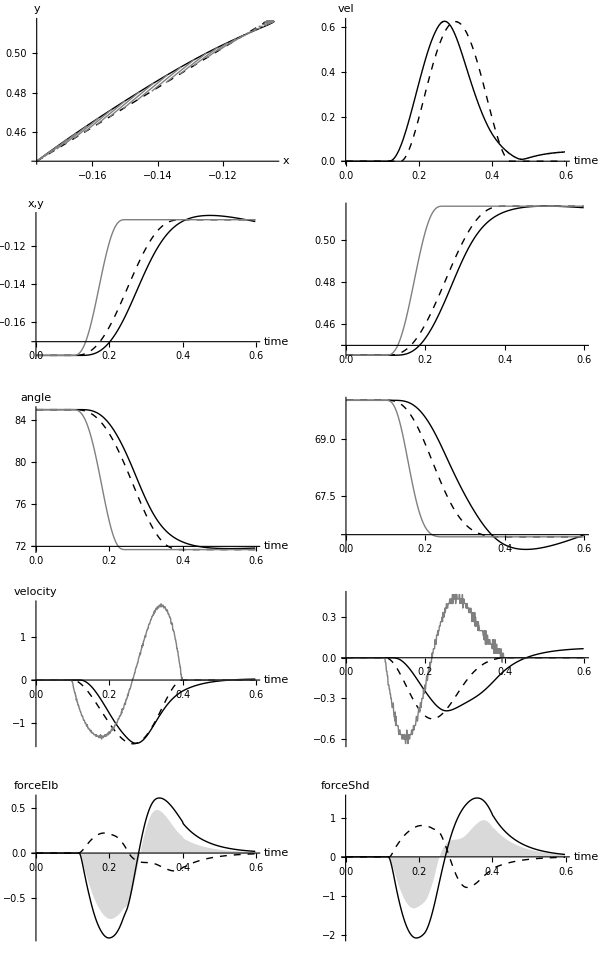

Reflex States

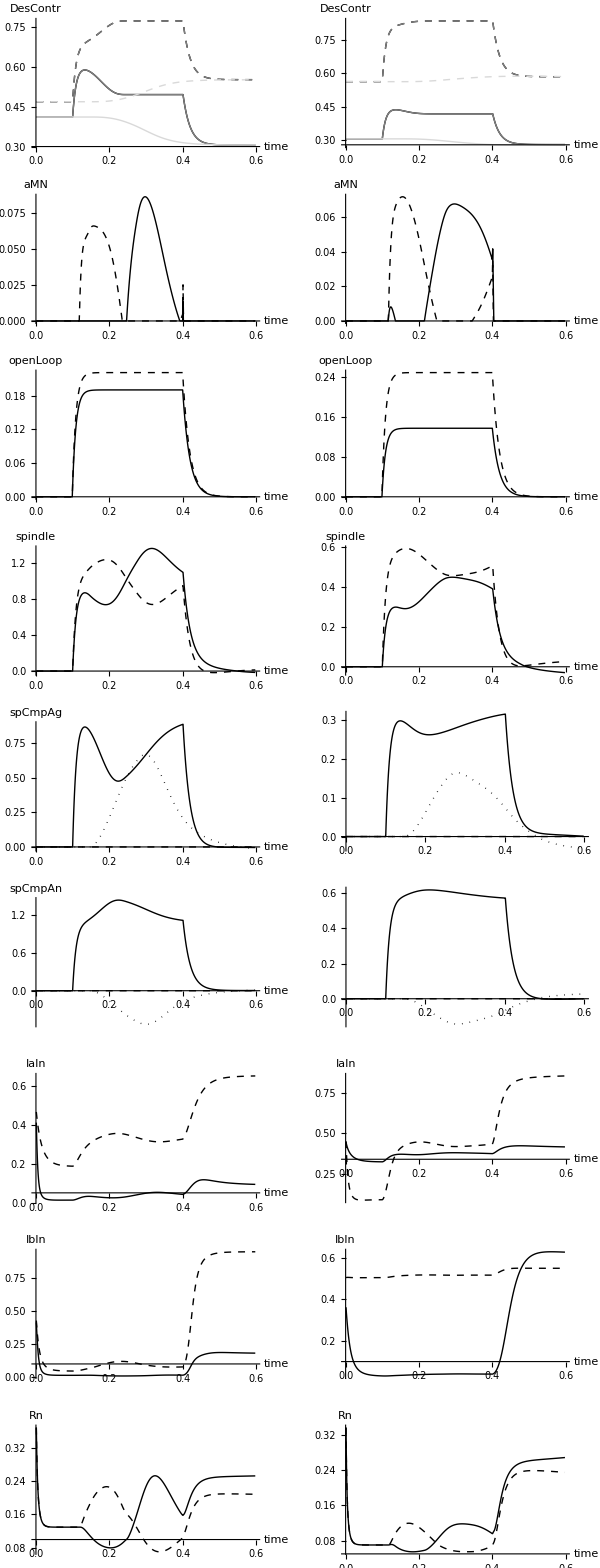

Muscle States

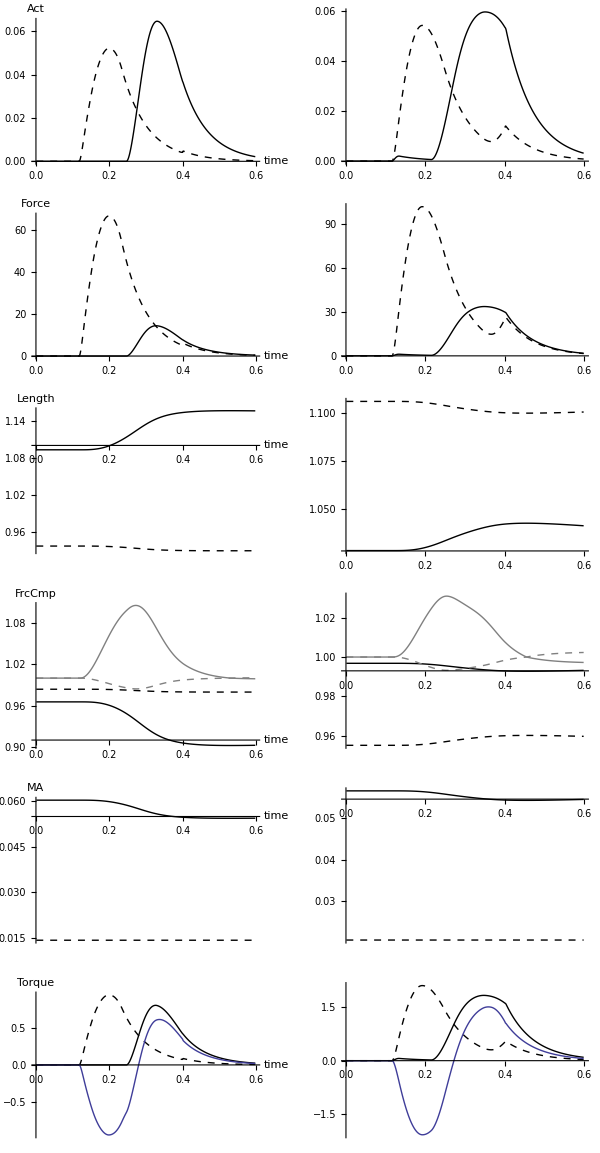

Phase space

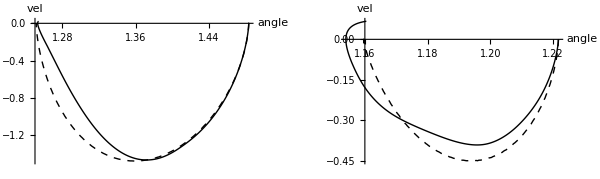

```mathematica
Print[Style["Arm States","Subtitle"]]
armPlots

Print[Style["Reflex States","Subtitle"]]
reflexPlots

Print[Style["Muscle States","Subtitle"]]
musclePlots

Print[Style["Phase space","Subtitle"]]
phSpacePlots
```

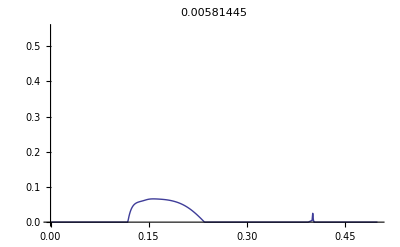

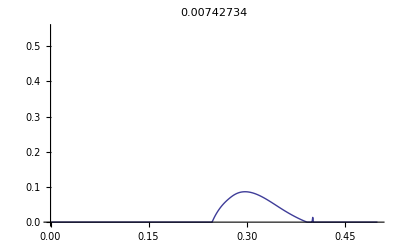

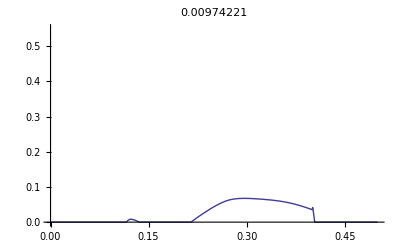

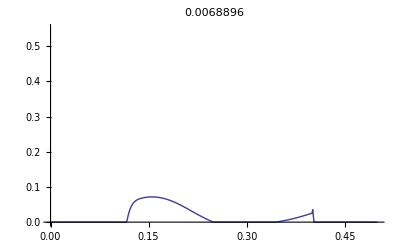

```mathematica
SetTrial[0];

ImpArea[tr_,var_,fr_,to_]:=Module[{},
SetTrial[tr];
s=NtoD[var];
s=s[[fr;;to]];
l=Length[s];
t = 0.001*Range[1,l];
d=ConstantArray[0.001,l];
ListLinePlot[Transpose[{t,s}],PlotRange->{Automatic,{0,0.55}},PlotLabel->Dot[d,s]]
];

ImpArea[0,"reflexElbMNAn",1,500]
ImpArea[0,"reflexElbMNAg",1,500]
ImpArea[0,"reflexShdMNAg",1,500]
ImpArea[0,"reflexShdMNAn",1,500]
```